Zadatak 1. Napisati program koji za dati skup čvorova kreira kubni prirodni splajn. Program testirati na skupu čvorova {(0,1),(1,2),(3,4),(3.8,6.8),(5,5),(6,3.2),(8,0.9)}.

```mathematica
cv={{0,1},{1,2},{3,4},{3.8,6.8},{5,5},{6,3.2},{8,0.9}};
```

```mathematica
koef[cv_]:=Module[{m,a,h,b},
m=Length[cv];
h=Table[cv[[i+1,1]]-cv[[i,1]],{i,1,m-1}];
a=Table[0,{i,1,m-2},{j,1,m-2}];
a[[1,1]]=2(h[[1]]+h[[2]]);
a[[1,2]]=h[[2]];
Do[
a[[i,i-1]]=h[[i]];
a[[i,i]]=2(h[[i]]+h[[i+1]]);
a[[i,i+1]]=h[[i+1]],
{i,2,m-3}];
a[[m-2,m-3]]=h[[m-3]];
a[[m-2,m-2]]=2(h[[m-3]]+h[[m-2]]);
b=Table[{0},{i,1,m-2}];
Do[
b[[i,1]]=3((cv[[i+2,2]]-cv[[i+1,2]])/(cv[[i+2,1]]-cv[[i+1,1]])-(cv[[i+1,2]]-cv[[i,2]])/(cv[[i+1,1]]-cv[[i,1]])),
{i,1,m-2}];
LinearSolve[a,b]
]
```

```mathematica
koef[cv]//MatrixForm
```

(-0.749686
2.24906
-4.49418
0.981238
0.175571)

```mathematica
sp16[cv_,tac_]:=Module[{m,n,koefc,h,c,a,b,d,rez},
m=Length[cv];
koefc=koef[cv];
h=Table[cv[[i+1,1]]-cv[[i,1]],{i,1,m-1}];
c[0]=0;
c[m-1]=0;
Do[
c[i]=koefc[[i,1]],
{i,1,m-2}];
Do[
a[i]=cv[[i+1,2]];
b[i]=(cv[[i+2,2]]-cv[[i+1,2]])/(cv[[i+2,1]]-cv[[i+1,1]])-h[[i+1]]/3(2c[i]+c[i+1]);
d[i]=(c[i+1]-c[i])/(3h[[i+1]]),
{i,0,m-2}];
Do[
If[cv[[i,1]]<=tac<=cv[[i+1,1]],
rez=a[i-1]+b[i-1](tac-cv[[i,1]])+c[i-1](tac-cv[[i,1]])^2+d[i-1](tac-cv[[i,1]])^3
],
{i,1,m-1}];
rez
]
```

```mathematica
sp16[cv,2.1]
```

2.30833

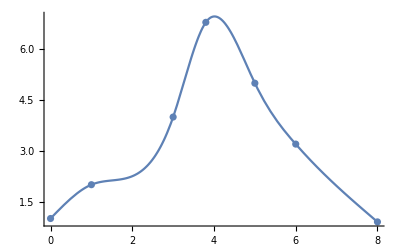

```mathematica
Show[ListPlot[cv],Plot[sp16[cv,x],{x,0,8}],PlotRange->All]
```